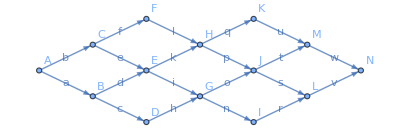

```mathematica
cpaGraph = EdgeTaggedGraph[{
"A" -> "B", "A" -> "C",
"B" -> "D", "B" -> "E",
"C" -> "E", "C" -> "F",
"D" -> "G",
"E" -> "G", "E" -> "H",
"F" -> "H",
"G" -> "I", "G" -> "J",
"H" -> "J", "H" -> "K",
"I" -> "L",
"J" -> "L", "J" -> "M",
"K" ->"M",
"L" -> "N",
"M" -> "N"
} -> {"a", "b", "c", "d", "e", "f", "h", "i", "k", "l", "n", "o", "p", "q", "r", "s", "t", "u", "v", "w"},
VertexLabels->"Name",
EdgeLabels->"EdgeTag", GraphLayout->{"SymmetricLayeredEmbedding", "Rotation"->90Degree}]
```

```mathematica
duration = <|
"A"->5,"B"->6,"C"->9,"D"->7,"E"->1,"F"->8,"G"->11,"H"->13,"I"->2,"J"->10,"K"->3,"L"->12,"M"->4,"N"->14|>
```

<|A→5,B→6,C→9,D→7,E→1,F→8,G→11,H→13,I→2,J→10,K→3,L→12,M→4,N→14|>

```mathematica
Successors[g_, v_] := VertexOutComponent[g, {v}, {1}]
Predecessors[g_, v_] := VertexInComponent[g, {v}, {1}]
```

```mathematica
Clear[esRec, efRec]
efRec[v_] := efRec[v] = esRec[v] + duration[v]
esRec[v_] := esRec[v] = 
If[
Predecessors[cpaGraph, v] === {}, 0,
Max[efRec[#] &/@Predecessors[cpaGraph, v]]]
```

```mathematica
es = AssociationMap[esRec, VertexList[cpaGraph]]
ef = AssociationMap[efRec, VertexList[cpaGraph]]
```

<|A→0,B→5,C→5,D→11,E→14,F→14,G→18,H→22,I→29,J→35,K→35,L→45,M→45,N→57|>

<|A→5,B→11,C→14,D→18,E→15,F→22,G→29,H→35,I→31,J→45,K→38,L→57,M→49,N→71|>

```mathematica
<|"A"->12,"B"->22,"C"->20,"D"->31,"E"->24,"F"->31,"G"->36,"H"->45,"I"->43,"J"->51,"K"->46,"L"->64,"M"->54,"N"->68|>
```

<|A→12,B→22,C→20,D→31,E→24,F→31,G→36,H→45,I→43,J→51,K→46,L→64,M→54,N→68|>

```mathematica
latestFinish = ef["N"]
```

71

```mathematica
Clear[lsRec, lfRec]
lsRec[v_] := lsRec[v] = lfRec[v] - duration[v]
lfRec[v_] := lfRec[v] = 
If[
Successors[cpaGraph, v] === {}, latestFinish,
Min[lsRec[#] &/@Successors[cpaGraph, v]]]
```

```mathematica
ls = AssociationMap[lsRec, VertexList[cpaGraph]]
lf = AssociationMap[lfRec, VertexList[cpaGraph]]
```

<|A→0,B→11,C→5,D→17,E→21,F→14,G→24,H→22,I→43,J→35,K→50,L→45,M→53,N→57|>

<|A→5,B→17,C→14,D→24,E→22,F→22,G→35,H→35,I→45,J→45,K→53,L→57,M→57,N→71|>

```mathematica
float = ls - es
```

<|A→0,B→6,C→0,D→6,E→7,F→0,G→6,H→0,I→14,J→0,K→15,L→0,M→8,N→0|>

{A,C,F,H,J,L,N}

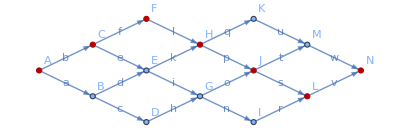

```mathematica
zeroFloat = Select[Normal[float], Last[#] === 0 &] // Map[First]
HighlightGraph[cpaGraph, zeroFloat]
```

```mathematica
es
ls
float
```

<|A→0,B→5,C→5,D→11,E→14,F→14,G→18,H→22,I→29,J→35,K→35,L→45,M→45,N→57|>

<|A→0,B→11,C→5,D→17,E→21,F→14,G→24,H→22,I→43,J→35,K→50,L→45,M→53,N→57|>

<|A→0,B→6,C→0,D→6,E→7,F→0,G→6,H→0,I→14,J→0,K→15,L→0,M→8,N→0|>